# Math 363 Homework 3

## Rachel Tjarksen

## Question 3

### Part (a)

A graphics grid resembling the first page in the knot table in the back of our book. Include the embedded text for standard knot notation ($3_1$, etc.), but omit the remaining data (e.g., 0.0,
{−4}(−1 1 0 1)), whose meaning we have not yet discussed. The required methods may be extracted from knots.nb

```mathematica
diagramentry[pair_]:=Graphics[{Thickness[.01],Blue,KnotData[pair,"KnotDiagramData"]}, 
Epilog -> Inset[Style[KnotData[pair,"AlexanderBriggsNotation"],Large],
{Right,Bottom},{Right,Bottom}]]
```

```mathematica
Grid[{{diagramentry[{3,1}],diagramentry[{4,1}],diagramentry[{5,1}],diagramentry[{5,2}],diagramentry[{6,1}],diagramentry[{6,2}],diagramentry[{6,3}],diagramentry[{7,1}]}}]
```

-Graphics-

```mathematica
Framed[GraphicsGrid[{{diagramentry[{3,1}],diagramentry[{4,1}],diagramentry[{5,1}],diagramentry[{5,2}],diagramentry[{6,1}],diagramentry[{6,2}],diagramentry[{6,3}],diagramentry[{7,1}]}}]]
```

-Graphics-

### Part (b)

A tricolored trefoil knot. This should be done “from scratch” using relatively short input (rather than just applying some “prepackaged” method). The idea is to first find an explicit parameterization   of such a trefoil plane curve (with three double points) using sine and cosine functions to define x(t), y(t). (An alternative is to use Polar Plot, with clear explanation of this plotting method.) Then figure out how to restrict the parameter range to three subintervals  , in order to create the required gaps for over/under crossings. (It may take a certain amount of trial and error to get gaps of suitable size, and preserving the three-fold rotational symmetry.) Then plot each strand in its own color (Red, Blue, Green), and combine into one plot.

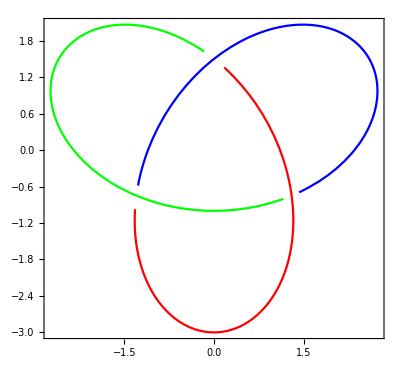

```mathematica
x[t]:=Sin[t]+2 Sin[2 t];
y[t]:=Cos[t]-2 Cos[2 t];

intervals={{-3.87,-1.87},{-1.78,0.24},{0.3,2.33}};
colors={Red,Green,Blue};

plot1=ParametricPlot[{x,y},{t,intervals[[1,1]],intervals[[1,2]]},PlotStyle->colors[[1]]];
plot2=ParametricPlot[{x,y},{t,intervals[[2,1]],intervals[[2,2]]},PlotStyle->colors[[2]]];
plot3=ParametricPlot[{x,y},{t,intervals[[3,1]],intervals[[3,2]]},PlotStyle->colors[[3]]];

Show[plot1,plot2,plot3,PlotRange->All,Axes->False,Frame->True,FrameStyle->Black]
```